## Lesson

Get first n elements of list:

```mathematica
Take[{a,b,c,d,e},3]
```

{a,b,c}

Take the n largest elements in list:

```mathematica
TakeLargest[Prime[Range[5]],3]
```

{11,7,5}

Take the n smallest elements in list:

```mathematica
TakeSmallest[Prime[Range[5]],3]
```

{2,3,5}

Take the n largest elements in list by applying a function:

```mathematica
TakeLargestBy[{"a","b","c","d","e"},LetterNumber[#]&,3]
```

{e,d,c}

Take the n smallest elements in list by applying a function:

```mathematica
TakeSmallestBy[{"a","b","c","d","e"},LetterNumber[#]&,3]
```

{a,b,c}

Get indices of appearances of element in list:

```mathematica
Position[{a,a,b,a,b},b]
```

{{3},{5}}

Replace elements at index positions with expression:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},3->x]
```

{a,b,x,d,e,f,g}

List element that is automatically removed:

```mathematica
{Nothing}
```

{}

## Questions

Q1. Find the last 5 digits in 2^1000.

```mathematica
IntegerDigits[2^1000][[-5;;]]
```

{6,9,3,7,6}

Q2. Pick out letters 10 through 20 in the alphabet.

```mathematica
FromLetterNumber/@Range[10,20]
```

{j,k,l,m,n,o,p,q,r,s,t}

Q3. Make a list of the letters at even-numbered positions in the alphabet.

```mathematica
FromLetterNumber/@Range[2,26,2]
```

{b,d,f,h,j,l,n,p,r,t,v,x,z}

Q4. Make a line plot of the second to last digit in the first 100 powers of 12.

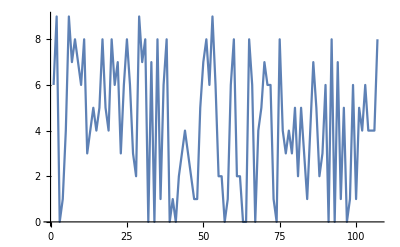

```mathematica
ListLinePlot[IntegerDigits[12^#&/@Range[100]][[-2]]]
```

Q5. Join lists of the first 20 squares and cubes, and get the 10 smallest elements of the combined list.

```mathematica
TakeSmallest[Join[Range[20]^2,Range[20]^3],10]
```

{1,1,4,8,9,16,25,27,36,49}

Q6. Find the positions of the word “software” in the Wikipedia entry for “computers”.

```mathematica
Flatten[Position[TextWords[WikipediaData["computer"]],"software"]]
```

{62,6063,6157,6179,6919,6941,6944,6948,6962,8165,8266,8273,8281,8303}

Q7. Make a histogram of where the letter “e” occurs in the words in WordList[ ].

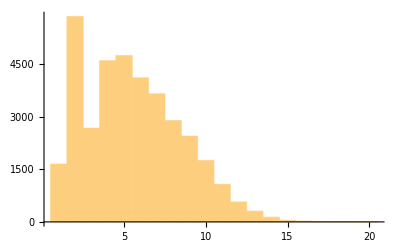

```mathematica
Histogram[Flatten[Position[Characters[#],"e"]&/@WordList[]]]
```

Q8. Make a list of the first 100 cubes, with every one whose position is a square replaced by Red.

```mathematica
ReplacePart[Range[100]^3,Thread[Range[10]^2->Red]]
```

{RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]}

Q9. Make a list of the first 100 primes, dropping ones whose first digit is less than 5.

```mathematica
If[IntegerDigits[#][[1]]<5,Nothing,#]&/@Prime[Range[100]]
```

{5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541}

Q10. Make a grid starting with Range[10], then at each of 9 steps randomly removing another element.

```mathematica
Grid[NestList[ReplacePart[#,RandomChoice[{1,Length[#]}]->Nothing]&,Range[10],9]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 |  | 
2 | 3 | 4 | 5 | 6 | 7 | 8 |  |  | 
3 | 4 | 5 | 6 | 7 | 8 |  |  |  | 
3 | 4 | 5 | 6 | 7 |  |  |  |  | 
4 | 5 | 6 | 7 |  |  |  |  |  | 
5 | 6 | 7 |  |  |  |  |  |  | 
6 | 7 |  |  |  |  |  |  |  | 
7 |  |  |  |  |  |  |  |  |

Q11. Find the longest 10 words in WordList[ ].

```mathematica
TakeLargestBy[WordList[],StringLength,10]
```

{electroencephalographic,electroencephalograph,counterrevolutionary,buckminsterfullerene,compartmentalization,electroencephalogram,internationalization,uncharacteristically,magnetohydrodynamics,incomprehensibility}

Q12. Find the 5 longest integer names for integers up to 100.

```mathematica
TakeLargestBy[IntegerName[Range[100]],StringLength,5]
```

{seventy-seven,seventy-three,seventy-eight,twenty-three,twenty-eight}

Q13. Find the 5 English names for integers up to 100 that have the largest number of “e”s in them.

```mathematica
TakeLargestBy[IntegerName[Range[100]],Count[Characters[#],"e"]&,5]
```

{seventy-three,seventeen,seventy-seven,nineteen,eleven}